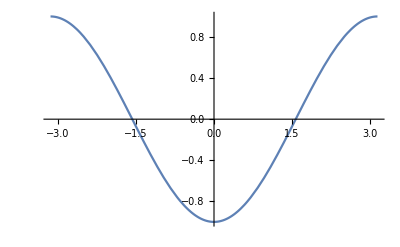

```mathematica
pot[x_]:=-Cos[x]
Plot[pot[x],{x,-π,π}]
```

```mathematica
(* set up the Levy alpha-stable SDE *)
α=1;
(* drift *)
(* f[x_] := Sin[x] *)
(* f[{x_,y_}]:={y,-Sin[x]}; *)
f[{x_,y_}]:={Sin[y],-pot'[x]}
(* constant diffusion *)
g=0.1;
```

```mathematica
-pot'[x]
```

-Sin[x]

```mathematica
(* phase plot for deterministic system *)
```

```mathematica
gettraj[i_]:=Block[
{mysol},mysol=NDSolve[{{x'[t],y'[t]}==f[{x[t],y[t]}],{x[0],y[0]}==ic[[i]]},{x[t],y[t]},{t,0,16π},PrecisionGoal->16];
ParametricPlot[{x[t],y[t]}/.mysol,{t,0,16π},PlotRange->{{-3,3},{-2,2}}]
]
```

```mathematica
numtraj=15;
ic=Table[{-3.0+ (i-1) 6/(numtraj-1),-2.0+4 (j-1)/(numtraj-1)},{i,1,numtraj},{j,1,numtraj}];
ic=Flatten[ic,1];
nic=Length[ic];
```

```mathematica
trajectories=Table[gettraj[i],{i,1,nic}];
```

```mathematica
phaseplot=Show[trajectories]
```

-Graphics-

```mathematica
cf=Compile[{{x,_Real,1}},f[x]]
```

CompiledFunction[…]

```mathematica
ntraj=100;
nsamp=1;
(* plots=Table[{},{i,ntraj}]; *)
dt = 0.0001;
ns = 400000;
tvec=Table[j*dt,{j,0,ns}];
For[traj=1,traj≤ntraj,traj+=1,
mcsol=Table[{0,0},ns+1];
ic={RandomVariate[NormalDistribution[0,1/3],1][[1]],0.0};
dlmat=Transpose[{RandomVariate[StableDistribution[1,α,0.0,0.0,(dt)^(1/α) g],ns],
RandomVariate[StableDistribution[1,α,0.0,0.0,(dt)^(1/α)g],ns]}];
mcsol=FoldList[#1 + dt cf[#1]+#2 &,ic,dlmat];
(*For[i=1,i≤ns,i+=1,mcsol[[i+1]] =mcsol[[i]]+ (dt*f[mcsol[[i]]] +  dlmat[[i]]);
]; *)
fname=StringJoin["mcsolsin2d",ToString[traj],".dat"];
myfile=OpenWrite[fname,BinaryFormat->True];
BinaryWrite[myfile,mcsol,"Real64"];
Close[myfile];Print[fname]
(* plots[[traj]]=ListPlot[mcsol]; *)
]
```

mcsolsin2d1.dat

mcsolsin2d2.dat

mcsolsin2d3.dat

mcsolsin2d4.dat

mcsolsin2d5.dat

mcsolsin2d6.dat

mcsolsin2d41.dat

mcsolsin2d7.dat

mcsolsin2d8.dat

mcsolsin2d9.dat

mcsolsin2d10.dat

mcsolsin2d11.dat

mcsolsin2d12.dat

mcsolsin2d13.dat

mcsolsin2d14.dat

mcsolsin2d15.dat

mcsolsin2d16.dat

mcsolsin2d17.dat

mcsolsin2d18.dat

mcsolsin2d19.dat

mcsolsin2d20.dat

mcsolsin2d21.dat

mcsolsin2d22.dat

mcsolsin2d23.dat

mcsolsin2d24.dat

mcsolsin2d25.dat

mcsolsin2d26.dat

mcsolsin2d27.dat

mcsolsin2d28.dat

mcsolsin2d29.dat

mcsolsin2d30.dat

mcsolsin2d31.dat

mcsolsin2d32.dat

mcsolsin2d33.dat

mcsolsin2d34.dat

mcsolsin2d35.dat

mcsolsin2d36.dat

mcsolsin2d37.dat

mcsolsin2d38.dat

mcsolsin2d39.dat

mcsolsin2d40.dat

mcsolsin2d42.dat

mcsolsin2d43.dat

mcsolsin2d44.dat

mcsolsin2d45.dat

mcsolsin2d46.dat

mcsolsin2d47.dat

mcsolsin2d48.dat

mcsolsin2d49.dat

mcsolsin2d50.dat

mcsolsin2d51.dat

mcsolsin2d52.dat

mcsolsin2d53.dat

mcsolsin2d54.dat

mcsolsin2d55.dat

mcsolsin2d56.dat

mcsolsin2d57.dat

mcsolsin2d58.dat

mcsolsin2d59.dat

mcsolsin2d60.dat

mcsolsin2d61.dat

mcsolsin2d62.dat

mcsolsin2d63.dat

mcsolsin2d64.dat

mcsolsin2d65.dat

mcsolsin2d66.dat

mcsolsin2d67.dat

mcsolsin2d68.dat

mcsolsin2d69.dat

mcsolsin2d70.dat

mcsolsin2d71.dat

mcsolsin2d72.dat

mcsolsin2d73.dat

mcsolsin2d74.dat

mcsolsin2d75.dat

mcsolsin2d76.dat

mcsolsin2d77.dat

mcsolsin2d78.dat

mcsolsin2d79.dat

mcsolsin2d80.dat

mcsolsin2d81.dat

mcsolsin2d82.dat

mcsolsin2d83.dat

mcsolsin2d84.dat

mcsolsin2d85.dat

mcsolsin2d86.dat

mcsolsin2d87.dat

mcsolsin2d88.dat

mcsolsin2d89.dat

mcsolsin2d90.dat

mcsolsin2d91.dat

mcsolsin2d92.dat

mcsolsin2d93.dat

mcsolsin2d94.dat

mcsolsin2d95.dat

mcsolsin2d96.dat

mcsolsin2d97.dat

mcsolsin2d98.dat

mcsolsin2d99.dat

mcsolsin2d100.dat